# Molecular Dynamics

## Colinear dynamics

```mathematica
Vlj[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
(*Flj[r_]=4 ϵ(12(σ^12/r^13)-6(σ^6/r^7));*)
Flj[r_]=24 ϵ(2(σ^12/r^13)-(σ^6/r^7));
```

```mathematica
ϵ=1;σ=1;m=1;
```

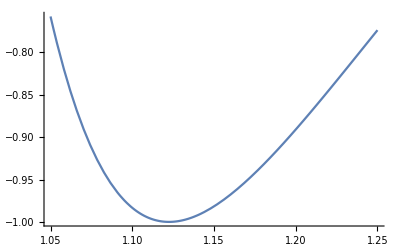

```mathematica
rMin=1.05;rMax=1.25;
Plot[Vlj[r],{r,rMin,rMax}]
```

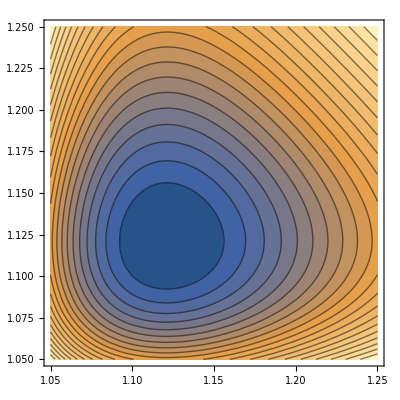

```mathematica
V[rAB_,rBC_]=Vlj[rAB]+Vlj[rBC]+Vlj[rAB+rBC];
VPlot=ContourPlot[V[rAB,rBC],{rAB,rMin,rMax},{rBC,rMin,rMax},Contours->20]
```

```mathematica
r0=rAB/.FindMinimum[V[rAB,rBC],{rAB,1.1},{rBC,1.1}][[2]]
```

1.12103

```mathematica
F[rAB_,rBC_]={
-Flj[rAB]-Flj[rAB+rBC],
Flj[rAB]-Flj[rBC],
Flj[rAB+rBC]+Flj[rBC]
};
F[r0,r0]
```

{2.01772×10^-8,0.,-2.01772×10^-8}

```mathematica
dx=0.001;
numHess=-{
(F[r0-dx,r0]-F[r0,r0]),
(F[r0+dx,r0-dx]-F[r0,r0]),
(F[r0,r0+dx]-F[r0,r0])
}/(dx m);
numHess//MatrixForm
```

(58.9887 | -59.2446 | 0.255859
-58.1511 | 117.396 | -59.2446
0.254968 | -58.1511 | 57.8961)

```mathematica
anaHess=D[V[xB-xA,xC-xB],{{xA,xB,xC},2}]/.{xA->-r0,xB->0,xC->r0};
anaHess//MatrixForm
```

(58.4395 | -58.695 | 0.255413
-58.695 | 117.39 | -58.695
0.255413 | -58.695 | 58.4395)

```mathematica
{eigVal,eigVec}=Eigensystem[anaHess];
eigVal;
freq=Sqrt[eigVal]
eigVec
```

{13.2697,7.62785,3.76973×10^-7}

{{0.408248,-0.816497,0.408248},{0.707107,-1.13668×10^-15,-0.707107},{0.57735,0.57735,0.57735}}

```mathematica
Sqrt[58.44]
Sqrt[3]Sqrt[58.44]
```

7.64461

13.2408

```mathematica
time=50;
dt=0.01;
nSteps=Round[time/dt]
```

5000

```mathematica
mode=3;
dx=0.01;
(*xA[0]=-r0+eigVec[[mode]][[1]]dx;
xB[0]=0+eigVec[[mode]][[2]]dx;
xC[0]=r0+eigVec[[mode]][[3]]dx;*)
xA[0]=-r0+0.02;
xB[0]=0;
xC[0]=r0;
vA[0]=0;
vB[0]=0;
vC[0]=0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]];
fB[0]=Flj[xB[0]-xA[0]]-Flj[xC[0]-xB[0]];
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]];
For[n=0,n<=nSteps,n++,
xA[n+1]=xA[n]+vA[n]dt+dt^2 fA[n]/(2m);
xB[n+1]=xB[n]+vB[n]dt+dt^2 fB[n]/(2m);
xC[n+1]=xC[n]+vC[n]dt+dt^2 fC[n]/(2m);
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]];
fB[n+1]=Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xB[n+1]];
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]];
vA[n+1]=vA[n]+(1/2)(fA[n]+fA[n+1])(dt/m);
vB[n+1]=vB[n]+(1/2)(fB[n]+fB[n+1])(dt/m);
vC[n+1]=vC[n]+(1/2)(fC[n]+fC[n+1])(dt/m);
]
```

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->White];
```

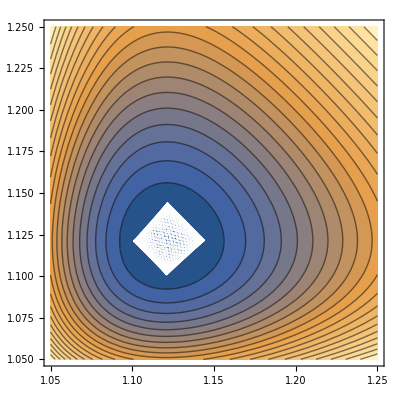

```mathematica
Show[VPlot,trajPlot]
```

```mathematica
Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-2.5,2.5},{-1,1}}],{n,0,nSteps,1}]
```

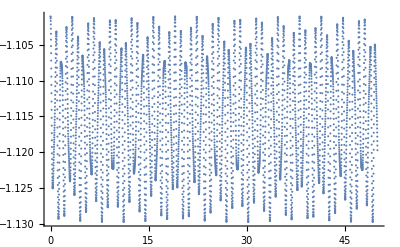

```mathematica
xData=Table[{n dt,xA[n]},{n,0,nSteps}];
ListPlot[xData]
```

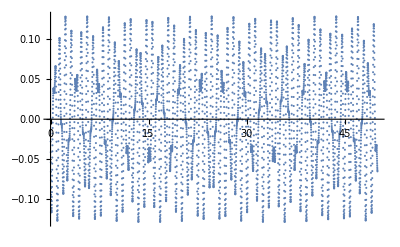

```mathematica
vData=Table[{n dt,vA[n]},{n,0,nSteps}];
ListPlot[vData]
```

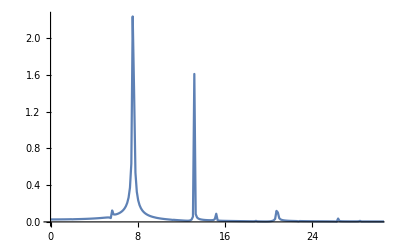

```mathematica
fRawData=Abs[Fourier[vData[[All,2]]]];
fData=Table[{(n-1) 2Pi/time,fRawData[[n]]},{n,1,nSteps}];
ListPlot[fData,PlotRange->{{0,30},All},Joined->True]
```